```mathematica
meanValues
```

{-0.0000926683,-0.000447012,-0.000475977,-0.000113285,-0.000669484,2.65909×10^-6,0.000249241,0.000304715,0.0000223666,0.000065161,0.000139742,0.000181184,-0.0000174411,0.0000225303,0.0000149601,-0.0000192739,-8.17072×10^-6,-0.0000826607,-0.000141641,-0.000156052,0.000255471,0.00013238,0.000135028,0.00015036,0.0000720019,0.0000279602,0.0000161016,0.0000475899,-0.000171523,-0.0000831666,1.36484×10^-6,0.0000450202,0.000606731,0.000206935,0.000198026,0.000218126,-0.000141164,-0.000129613,-0.000123735,-0.000126959}

```mathematica
nplots
```

4

```mathematica
Length[PP]
```

10

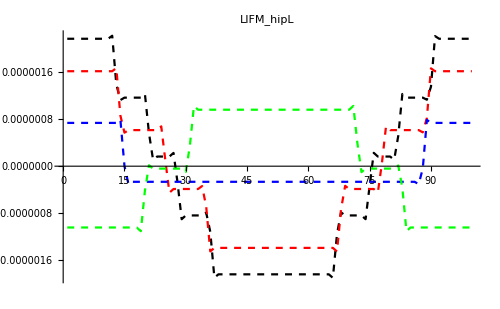

```mathematica
ListLinePlot[plotDATA,PlotStyle->colors,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[1]]},{-meanValues[[1]],1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotLabel->label,ImageSize->size,PlotRange->All]
```

```mathematica
plotDATA//Dimensions
```

{4,100,2}

```mathematica
plotDATA[[1]]
```

```mathematica
nplots
```

4

```mathematica
ColorSetter[Black]
```

```mathematica
colors
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
A={a,b,c,d};
B={1,2,3,4};
```

{{-Graphics-,Thickness[0.01]},{-Graphics-,Thickness[0.01]},{-Graphics-,Thickness[0.01]},{-Graphics-,Thickness[0.1]}}

```mathematica
Thread[{A,B}]
```

{{a,1},{b,2},{c,3},{d,4}}

```mathematica
(*blue/thick,grey/thick,red/thin,lightgreen/thin*)
```

```mathematica
meanValues
```

{-0.000141164,-0.000129613,-0.000123735,-0.000126959}

```mathematica
iconDirectory="/Users/chrisrichards/Desktop/FrogWork/FrogPubs/kassinaMJ";
SetDirectory[iconDirectory];
pelvicLeftIcon=Import["pelvisLeft_icon.png"];
pelvicRightIcon=Import["pelvisRight_icon.png"];
pelvicCenterIcon=Import["pelvisCenter_icon.png"];
ResetDirectory[];
```

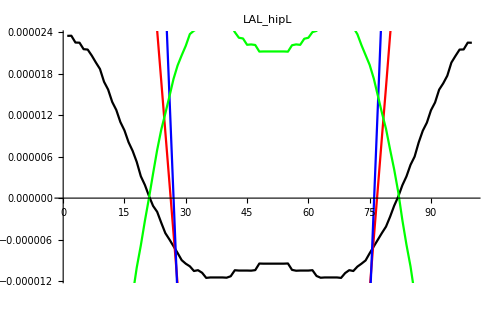

```mathematica
Show[Table[
ListLinePlot[plotDATA[[k]],PlotStyle->colors[[k]],MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[k]]},{-meanValues[[k]],1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotLabel->label,ImageSize->size,PlotRange->All]
,{k,1,nplots}]]
```

```mathematica
meanVALUES//Dimensions
```

{10,4}

```mathematica
meanLabel=DisplayForm[FrameBox[ToString[meanVALUES[[1,1]]]]];
(*muslabelPlot=(PlotLabel/.AbsoluteOptions[PPrel[[1]],PlotLabel]);*)
(*plotlabel=muslabelPlot<>"\n"<>meanLabel;*)
Show[PPrel[[1]],PlotRange->scaledRange(*,PlotLabel->plotlabel*),Epilog->
Inset[Row[{Style["Akjhg",Red],Style["B",Blue]}],{Center,Bottom},{Center,Bottom}]

]
```

-Graphics-

```mathematica
vectorToString[vector_]:=StringReplace[ToString[vector],{","->" ","{"->"","}"->""}]
```

StringJoin::string: String expected at position 2 in LIE_hipL
.

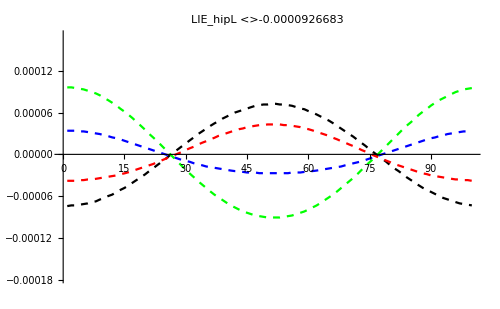

```mathematica
Epi
```

```mathematica
(PlotLabel/.AbsoluteOptions[PPrel[[1]],PlotLabel])
```

LIE_hipL

```mathematica
muslabel
```

LIFM

```mathematica
Row[{Style["Akjhg",Red],Style["B",Blue]}]
```

AkjhgB

```mathematica
wAB="AB"
```

AB

```mathematica
Framed[StringReplace[" asfkasaskmflasafasknaslgvnac ",#->ToString[Style[#,Red],StandardForm]&/@{"mfl","nas"}]]
```

asfkasaskmflasafasknaslgvnac

```mathematica
vectorToString[vector_]:=StringReplace[ToString[vector],{","->" ","{"->"","}"->""}]
```

-0.0000926683  -0.000447012  -0.000475977  -0.000113285

```mathematica
(*complicated code to generate box of coloured text values for mean values*)
meanString=vectorToString[meanVALUES[[1]]];
Do[
meanString=StringReplace[meanString,#->ToString[Style[#,colors[[m]]],StandardForm]&/@{ToString[meanVALUES[[1,m]]]}]
,{m,1,nplots}];
```

```mathematica
Framed[meanString]
```

-0.0000926683  -0.000447012  -0.000475977  -0.000113285

```mathematica
ToString[meanVALUES[[1,1]]]
```

-0.0000926683

```mathematica
meanString
```

-0.0000926683  -0.000447012  -0.000475977  -0.000113285

```mathematica
ToString[meanVALUES[[1,1]]]
```

-0.0000926683

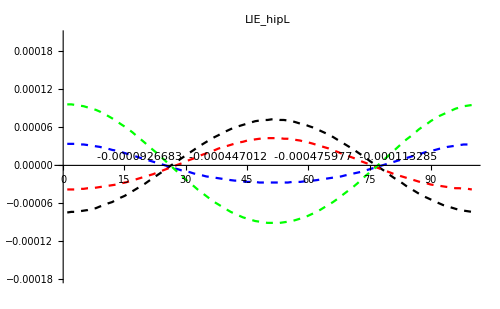

```mathematica
(*complicated code to generate box of coloured text values for mean values*)
meanString=vectorToString[meanVALUES[[1]]];
Do[
meanString=StringReplace[meanString,#->ToString[Style[#,colors[[m]]],StandardForm]&/@{ToString[meanVALUES[[1,m]]]}]
,{m,1,nplots}];
meanLabel=Framed[meanString,Background->LightYellow,FrameStyle->Opacity[0.1]];

Show[PPrel[[1]],PlotRange->scaledRange,Epilog->{
Inset[meanLabel,Scaled[{0.5,0.5}]],Inset[pelvicRightIcon,Scaled[{0.1,0.9}],Scaled[{0.5,0.5}],5],
Inset[pelvicCenterIcon,Scaled[{0.5,0.9}],Scaled[{0.5,0.5}],5],
Inset[pelvicLeftIcon,Scaled[{0.9,0.9}],Scaled[{0.5,0.5}],5]
}]
```

```mathematica
Epi
```

```mathematica
Framed[meanString,Background->LightYellow,FrameStyle->Opacity[0]]
```

-0.0000926683  -0.000447012  -0.000475977  -0.000113285

```mathematica
scaledRange
```

{{0.,100.},{-0.000177531,0.000187543}}

```mathematica
lineStyles[[4]]
```

{-Graphics-,Thickness[0.002]}

```mathematica
trials
```

{1,2,3,4}

```mathematica
lineStyles[[4]]
```

{-Graphics-,Thickness[0.002]}

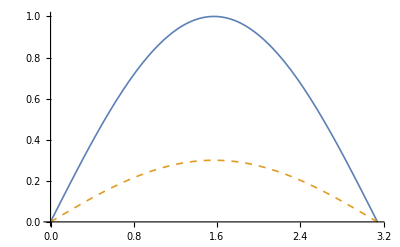

```mathematica
Plot[{Sin[x],.3*Sin[x]},{x,0,Pi},PlotStyle->{plotweight,{plotweight,Dashed}}]
```

```mathematica
plotweight
```

Thickness[0.003]

```mathematica
colorStr
```

{Blue,Grey,Red,Light Green}

```mathematica
nplots
```

3

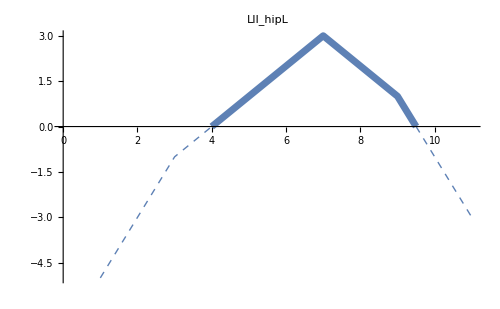

```mathematica
ListLinePlot[{-5,-3,-1,0,1,2,3,2,1,-1,-3},MeshFunctions->{#2&},Mesh->{{-1000,0},{0,1000}},MeshShading->{Thickness[0.01],Directive[Dashed,Thickness[0.002]]},MeshStyle->None,PlotLabel->label,ImageSize->size,PlotRange->All]
```

```mathematica
dataResample[TmaDATAraw[[;;,3]],npoints]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
scaledRange
```

{{0.,100.},{-0.133368,0.224765}}

```mathematica
ymax
```

0.187304

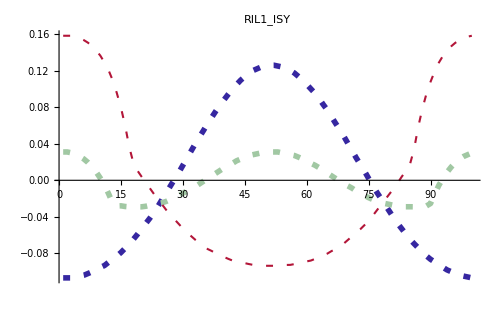

```mathematica
Show[plotrel,PlotRange->All]
```

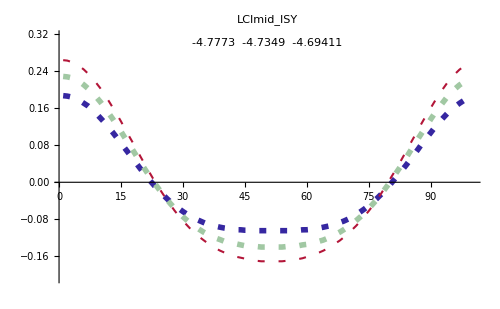

```mathematica
PP[[1]]
```

```mathematica
PPreordered=PP[[{2,4,1,3}]];
GraphicsGrid[Partition[PPreordered,2]]
```

```mathematica
GraphicsGrid[{{PP[[2]],PP[[4]]},{PP[[1]],PP[[3]]}}]
```